```mathematica
Входные данные:
```

```mathematica
|I|=6
```

```mathematica
|U|=12
```

```mathematica
U={1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5}
```

```mathematica
b={7,4,-1,-7,-2,-1}
```

```mathematica
{Subscript[λ, 1,5]->-4,Subscript[λ, 1,5]^2->-8,Subscript[λ, 1,5]^3->-7,Subscript[λ, 2,5]->1,Subscript[λ, 2,5]^2->-2,Subscript[λ, 2,5]^3->-1,Subscript[λ, 3,1]->-7,Subscript[λ, 3,1]^2->3,Subscript[λ, 3,1]^3->4,Subscript[λ, 3,4]->8,Subscript[λ, 3,4]^2->-4,Subscript[λ, 3,4]^3->-5,Subscript[λ, 3,5]->5,Subscript[λ, 3,5]^2->6,Subscript[λ, 3,5]^3->5,Subscript[λ, 4,1]->8,Subscript[λ, 4,1]^2->9,Subscript[λ, 4,1]^3->7,Subscript[λ, 4,2]->7,Subscript[λ, 4,2]^2->10,Subscript[λ, 4,2]^3->11,Subscript[λ, 4,6]->-1,Subscript[λ, 4,6]^2->1,Subscript[λ, 4,6]^3->2,Subscript[λ, 5,4]->-6,Subscript[λ, 5,4]^2->3,Subscript[λ, 5,4]^3->4,Subscript[λ, 6,2]->-1,Subscript[λ, 6,2]^2->9,Subscript[λ, 6,2]^3->10,Subscript[λ, 6,3]->0,Subscript[λ, 6,3]^2->5,Subscript[λ, 6,3]^3->6,Subscript[λ, 6,5]->-6,Subscript[λ, 6,5]^2->-2,Subscript[λ, 6,5]^3->-4}
```

```mathematica
{Subscript[α, 3]->3,Subscript[α, 2]->7,Subscript[α, 1]->-1}
```

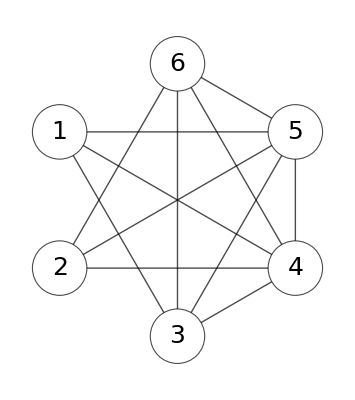

```mathematica
Исходный граф:
```

```mathematica
Любое частное решение:
```

{(x̃)_(1,5)→0,(x̃)_(2,5)→4,(x̃)_(3,1)→-7,(x̃)_(3,4)→0,(x̃)_(3,5)→0,(x̃)_(4,1)→0,(x̃)_(4,2)→0,(x̃)_(4,6)→-5,(x̃)_(5,4)→2,(x̃)_(6,2)→0,(x̃)_(6,3)→-6,(x̃)_(6,5)→0}

```mathematica
Табличная форма:
```

(x̃)_(1,5)→0
(x̃)_(2,5)→4
(x̃)_(3,1)→-7
(x̃)_(3,4)→0
(x̃)_(3,5)→0
(x̃)_(4,1)→0
(x̃)_(4,2)→0
(x̃)_(4,6)→-5
(x̃)_(5,4)→2
(x̃)_(6,2)→0
(x̃)_(6,3)→-6
(x̃)_(6,5)→0

```mathematica
Проверка частного решения(Simplify):
```

{True,True,True,True,True,True}

```mathematica
Un = {1->5,3->4,3->5,4->1,4->2,6->2,6->5}
```

```mathematica
Ut = {3->1,6->3,4->6,5->4,2->5}
```

```mathematica
deltas:
```

{δ_(1,5)^(1->5)→0,δ_(5,4)^(1->5)→1,δ_(4,6)^(1->5)→1,δ_(6,3)^(1->5)→1,δ_(3,1)^(1->5)→1,δ_(3,4)^(3->4)→0,δ_(4,6)^(3->4)→1,δ_(6,3)^(3->4)→1,δ_(3,5)^(3->5)→0,δ_(5,4)^(3->5)→1,δ_(4,6)^(3->5)→1,δ_(6,3)^(3->5)→1,δ_(4,1)^(4->1)→0,δ_(4,6)^(4->1)→-1,δ_(6,3)^(4->1)→-1,δ_(3,1)^(4->1)→-1,δ_(4,2)^(4->2)→0,δ_(2,5)^(4->2)→1,δ_(5,4)^(4->2)→1,δ_(6,2)^(6->2)→0,δ_(2,5)^(6->2)→1,δ_(5,4)^(6->2)→1,δ_(4,6)^(6->2)→1,δ_(6,5)^(6->5)→0,δ_(5,4)^(6->5)→1,δ_(4,6)^(6->5)→1}

```mathematica
Детерменанты:
{{, 1->5, 3->4, 3->5, 4->1, 4->2, 6->2, 6->5}, {Subscript[Δ, τρ], -18, 7, -2, 16, 2, -7, -13}, {Subscript[Δ, τρ]^2, 4, 2, 15, 0, 11, 11, 2}, {Subscript[Δ, τρ]^3, 9, 3, 17, -5, 14, 15, 2}}
```

```mathematica
Uс = {1->5,3->4,3->5}
```

```mathematica
Un = {4->1,4->2,6->2,6->5}
```

```mathematica
Subscript[Δ, c] = {{16,2,-7},{0,11,11},{-5,14,15}}
```

```mathematica
А i-ые:
```

{A_1→-47,A_2→65,A_3→73}

```mathematica
betas=({{-47-16 Subscript[x, 4,1]-2 Subscript[x, 4,2]+7 Subscript[x, 6,2]+13 Subscript[x, 6,5]}, {65-11 Subscript[x, 4,2]-11 Subscript[x, 6,2]-2 Subscript[x, 6,5]}, {73+5 Subscript[x, 4,1]-14 Subscript[x, 4,2]-15 Subscript[x, 6,2]-2 Subscript[x, 6,5]}})
```

```mathematica
Subscript[x, c]={Subscript[x, 1,5]->1/319 (1610-319 Subscript[x, 4,1]-201 Subscript[x, 6,5]),Subscript[x, 3,4]->1/319 (-3062-319 Subscript[x, 4,2]+773 Subscript[x, 6,5]),Subscript[x, 3,5]->1/319 (4947-319 Subscript[x, 6,2]-831 Subscript[x, 6,5])}
```

```mathematica
Общее решение:
```

{x_(3,1)→-7-x_(4,1)+1/319 (1610-319 x_(4,1)-201 x_(6,5)),x_(6,3)→-6-x_(4,1)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+1/319 (-3062-319 x_(4,2)+773 x_(6,5)),x_(4,6)→-5-x_(4,1)+x_(6,2)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+x_(6,5)+1/319 (-3062-319 x_(4,2)+773 x_(6,5)),x_(5,4)→2+x_(4,2)+x_(6,2)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+x_(6,5),x_(2,5)→4+x_(4,2)+x_(6,2)}

```mathematica
В табличной форме:
```

x_(3,1)→-7-x_(4,1)+1/319 (1610-319 x_(4,1)-201 x_(6,5))
x_(6,3)→-6-x_(4,1)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+1/319 (-3062-319 x_(4,2)+773 x_(6,5))
x_(4,6)→-5-x_(4,1)+x_(6,2)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+x_(6,5)+1/319 (-3062-319 x_(4,2)+773 x_(6,5))
x_(5,4)→2+x_(4,2)+x_(6,2)+1/319 (4947-319 x_(6,2)-831 x_(6,5))+1/319 (1610-319 x_(4,1)-201 x_(6,5))+x_(6,5)
x_(2,5)→4+x_(4,2)+x_(6,2)

```mathematica
Проверка общего решения(Simplify):
```

{{True,True,True,True,True,True,True,True,True}}